# FindRandomGridMazeSolution

Find a solution to a random maze

## Definition

```mathematica
PositiveIntegerQ//ClearAll
PositiveIntegerQ[n_]:=And@@{IntegerQ[n],TrueQ[n∈PositiveIntegers]}
```

```mathematica
ClearAll[FindRandomGridMazeSolution]
```

```mathematica
FindRandomGridMazeSolution::usage="FindRandomGridMazeSolution[{m,n}] finds a solution and other data for a random grid maze of size m by n.";
FindRandomGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)}]:=Module[{randomSeed,start,end,g,maze,m,solvedmaze,shortestPath,shortestPathSubgraph,deadEnds,deadEndsCount,treeOutline},g=GridGraph[{m1,n1}];randomSeed=$RandomGeneratorState;m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=m1*n1(*Last@VertexList[m]*) (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];(*tree=GraphTree[maze];treeDepth=TreeDepth[tree];
treeLeaves=TreeLeaves[tree];
treeLeafCount=TreeLeafCount[tree];
treeSize=TreeSize[tree];*)
(*deadEnds=Complement[TreeLevel[tree,{-1}->"Data"],{end}];deadEndsCount=Length@deadEnds;treeOutline=TreeOutline[tree];*)shortestPathSubgraph=Subgraph[maze,shortestPath];<|"start"->start,"end"->end,"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph,"random-seed"->randomSeed(*"tree"->tree,"tree-depth"->treeDepth,"tree-leaves"->treeLeaves,"tree-leaf-count"->treeLeafCount,"tree-size"->treeSize*)(*"dead-ends"->deadEnds,"dead-ends-count"->deadEndsCount,"tree-outline"->treeOutline*)|>]
(*FindRandomGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)}]:=Module[{g,maze,m,solvedmaze,shortestPath,start,end,shortestPathSubgraph,tree,randomSeed,treeDepth,treeLeaves,treeLeafCount,treeSize,deadEnds,deadEndsCount,treeOutline},g=GridGraph[{m1,n1}];randomSeed=$RandomGeneratorState;m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=m1*n1(*Last@VertexList[m]*) (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];tree=GraphTree[maze];treeDepth=TreeDepth[tree];
treeLeaves=TreeLeaves[tree];
treeLeafCount=TreeLeafCount[tree];
treeSize=TreeSize[tree];deadEnds=Complement[TreeLevel[tree,{-1}->"Data"],{end}];deadEndsCount=Length@deadEnds;treeOutline=TreeOutline[tree];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"start"->start,"end"->end,"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph,"random-seed"->randomSeed,"tree"->tree,"tree-depth"->treeDepth,"tree-leaves"->treeLeaves,"tree-leaf-count"->treeLeafCount,"tree-size"->treeSize,"dead-ends"->deadEnds,"dead-ends-count"->deadEndsCount,"tree-outline"->treeOutline|>]
FindRandomGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)},"random-seed"]:=Module[{randomSeed},randomSeed=$RandomGeneratorState;SeedRandom[];<|"random-seed"->randomSeed|>]
FindRandomGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)},"start"]=<|"start"->1|>;
FindRandomGridMazeSolution[{m_?PositiveIntegerQ /;!(m<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges.*),n_?PositiveIntegerQ/;!(n<=1)(*equivalent to n>1*)},"end"]:=<|"end"->m n|>
FindRandomGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)},"maze"]:=Module[{g,maze,m,randomSeed},g=GridGraph[{m1,n1}];randomSeed=$RandomGeneratorState;m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;<|"maze"->maze|>]
FindRandomGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)},"solved-maze"]:=Module[{g,maze,m,randomSeed},g=GridGraph[{m1,n1}];randomSeed=$RandomGeneratorState;m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;<|"maze"->maze|>]
(*FindRandomGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1),n1_?PositiveIntegerQ/;!(n1<=1)},property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph","tree","random-seed","tree-depth","tree-leaves","tree-leaf-count","tree-size","dead-ends","dead-ends-count","tree-outline"})]]:=Module[{data},data=Lookup[BlockRandom@FindRandomGridMazeSolution[{m1,n1}],property];SeedRandom[];data]*)
(*FindRandomGridMazeSolution[{m1_?PositiveIntegerQ/;!(m1<=1),n1_?PositiveIntegerQ/;!(n1<=1)},property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph","tree","random-seed","tree-depth","tree-leaves","tree-leaf-count","tree-size","dead-ends","dead-ends-count","tree-outline"})]]:=Module[{data,properties,dependencies},properties={"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph","tree","random-seed","tree-depth","tree-leaves","tree-leaf-count","tree-size","dead-ends","dead-ends-count","tree-outline"};
dependencies=<|"maze"->{},"solved-maze"->{"maze","shortest-path"},"shortest-path"->{"maze"},"distance"->{"shortest-path"},"start"->{},"end"->{},"shortest-path-subgraph"->{"maze","shortest-path"},"tree"->{"maze"},"random-seed"->{},"tree-depth"->{"tree"},"tree-leaves"->{"tree"},"tree-leaf-count"->{"tree-leaves"},"tree-size"->{"tree"},"dead-ends"->{"maze"},"dead-ends-count"->{"dead-ends"},"tree-outline"->{"tree"}|>;
data=AssociationMap[p|->Lookup[BlockRandom@FindRandomGridMazeSolution[{m1,n1}],p]][Intersection[properties,property,dependencies[property]]];
SeedRandom[];
data]*)

FindRandomGridMazeSolution[{m1_?PositiveIntegerQ/;!(m1<=1),n1_?PositiveIntegerQ/;!(n1<=1)},property_?VectorQ]:=Module[{data},data=AssociationMap[p↦Lookup[BlockRandom@FindRandomGridMazeSolution[{m1,n1}],p]][Intersection[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph","tree","random-seed","tree-depth","tree-leaves","tree-leaf-count","tree-size","dead-ends","dead-ends-count","tree-outline"},property]];SeedRandom[];data]
FindRandomGridMazeSolution[{m1_?PositiveIntegerQ/;!(m1<=1),n1_?PositiveIntegerQ/;!(n1<=1)},"everything-except-trees-and-tree-leaves"]:=Module[{data},data=AssociationMap[p↦Lookup[BlockRandom@FindRandomGridMazeSolution[{m1,n1}],p]][{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph","random-seed","tree-depth","tree-leaf-count","tree-size","dead-ends","dead-ends-count","tree-outline"}];SeedRandom[];data]
FindRandomGridMazeSolution[args___]:=Null/;CheckArguments[FindRandomGridMazeSolution[args],{1,2}]*)
```

## Documentation

### Usage

FindRandomGridMazeSolution[{m,n}]

finds a solution to a random maze of size m by n.

FindRandomGridMazeSolution[{m,n},property]

computes property which can be a single string or a list of properties.

### Details & Options

How does this compare with https://resources.wolframcloud.com/FunctionRepository/resources/RandomMaze/ using the option "ShowSolution"-> True? 
Can you make an example comparing the two functions?
If the functionalities mainly overlap, we may reject this submission in favor of the existing resource function, unless you can show significant advantages in performance or functionality for your function.

I have added more functionality.

## Examples

### Basic Examples

Be sure to use delimiters between independent examples. I have added some below.

Find a solution to a random 3 × 3 maze:

```mathematica
FindRandomGridMazeSolution[{3,3}]
```

Association[start→start$443821,end→end$443821,maze→maze$443821,solved-maze→solvedmaze$443821,shortest-path→shortestPath$443821,distance→GraphDistance[m$443821,start$443821,end$443821],start→start$443821,end→end$443821,shortest-path-subgraph→shortestPathSubgraph$443821,random-seed→randomSeed$443821,Null]

```mathematica
{maze,randomSeed}=Values@FindRandomGridMazeSolution[{3,3},{"maze","random-seed"}];
```

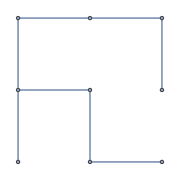

```mathematica
SeedRandom[randomSeed];
Graph[FindRandomGridMazeSolution[{3,3},"maze"],ImageSize->Small]
```

Get the solution:

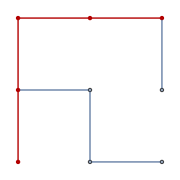

```mathematica
SeedRandom[randomSeed];
Graph[FindRandomGridMazeSolution[{3,3},"solved-maze"],ImageSize->Small]
```

Get data on the maze:

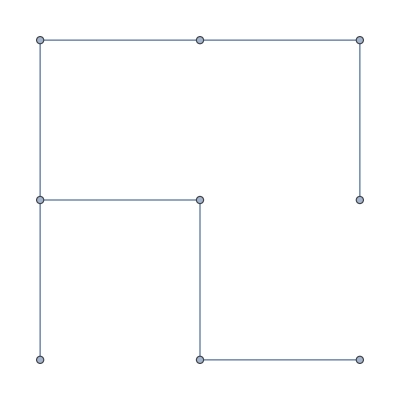
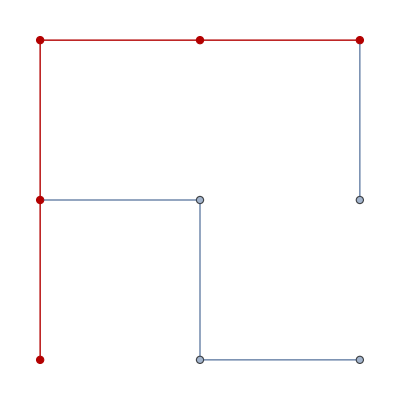
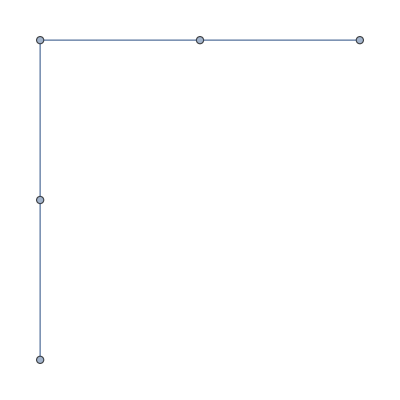
<|start→1,end→9,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→{1,2,3,6,9},distance→4,shortest-path-subgraph→-Graphics-,random-seed→RandomGeneratorState[…],tree→-Graphics-,tree-depth→5,tree-leaves→{-Graphics-,-Graphics-},tree-leaf-count→2,tree-size→9,dead-ends→{7,8},dead-ends-count→2,tree-outline→|>

```mathematica
SeedRandom[randomSeed];
FindRandomGridMazeSolution[{3,3}]
```

Find a solution to a random 5 × 5 maze:

```mathematica
{maze,randomSeed}=Values@FindRandomGridMazeSolution[{5,5},{"maze","random-seed"}];
```

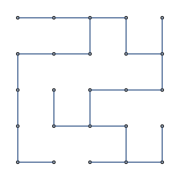

```mathematica
SeedRandom[randomSeed];
Graph[FindRandomGridMazeSolution[{5,5},"maze"],ImageSize->Small]
```

Get the solution:

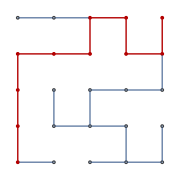

```mathematica
SeedRandom[randomSeed];
Graph[FindRandomGridMazeSolution[{5,5},"solved-maze"],ImageSize->Small]
```

Get data on the maze:

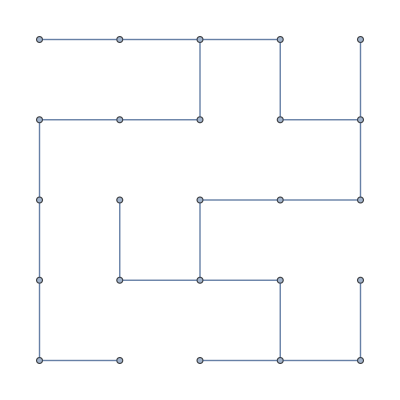
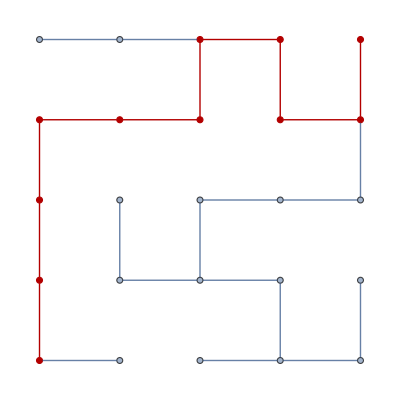
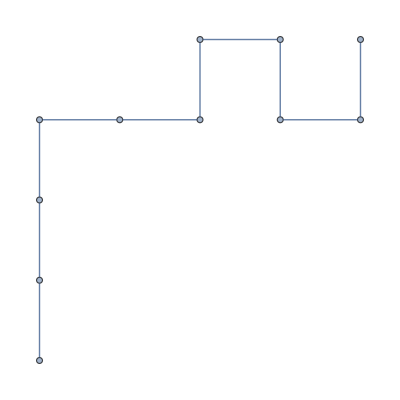
<|start→1,end→25,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→{1,2,3,4,9,14,15,20,19,24,25},distance→10,shortest-path-subgraph→-Graphics-,random-seed→RandomGeneratorState[…],tree→-Graphics-,tree-depth→17,tree-leaves→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},tree-leaf-count→6,tree-size→25,dead-ends→{5,6,8,11,22},dead-ends-count→5,tree-outline→|>

```mathematica
SeedRandom[randomSeed];
FindRandomGridMazeSolution[{5,5}]
```

Find a solution to a random 10 × 10 maze:

```mathematica
{maze,randomSeed}=Values@FindRandomGridMazeSolution[{10,10},{"maze","random-seed"}];
```

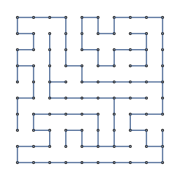

```mathematica
SeedRandom[randomSeed];
Graph[FindRandomGridMazeSolution[{10,10},"maze"],ImageSize->Small]
```

Get the solution:

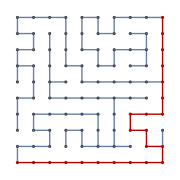

```mathematica
SeedRandom[randomSeed];
Graph[FindRandomGridMazeSolution[{10,10},"solved-maze"],ImageSize->Small]
```

Get data on the maze:

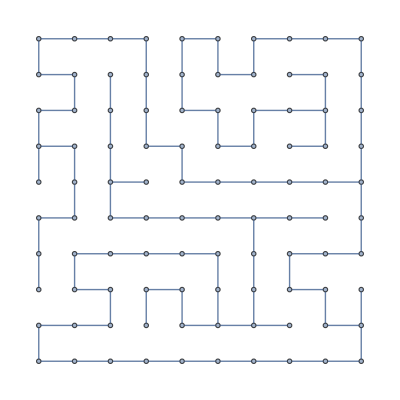
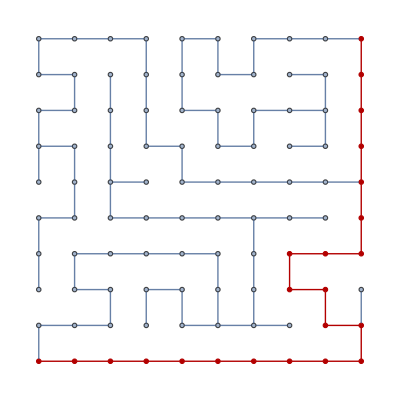
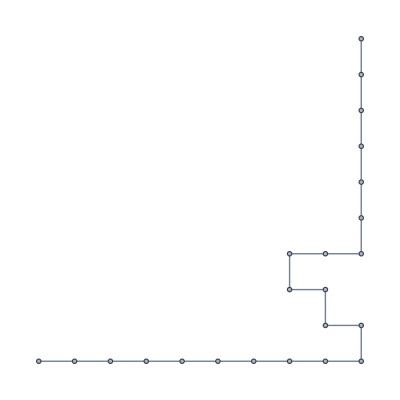
<|start→1,end→100,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→{1,11,21,31,41,51,61,71,81,91,92,82,83,73,74,84,94,95,96,97,98,99,100},distance→22,shortest-path-subgraph→-Graphics-,random-seed→RandomGeneratorState[…],tree→-Graphics-,tree-depth→42,tree-leaves→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},tree-leaf-count→10,tree-size→100,dead-ends→{3,6,29,32,36,72,77,79,85,93},dead-ends-count→10,tree-outline→|>

```mathematica
SeedRandom[randomSeed];
FindRandomGridMazeSolution[{10,10}]
```

Find a solution to a random 15 × 15 maze:

```mathematica
{maze,randomSeed}=Values@FindRandomGridMazeSolution[{15,15},{"maze","random-seed"}];
```

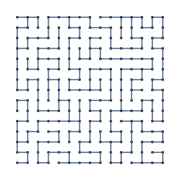

```mathematica
SeedRandom[randomSeed];
Graph[FindRandomGridMazeSolution[{15,15},"maze"],ImageSize->Small]
```

Get the solution:

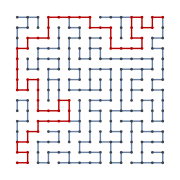

```mathematica
SeedRandom[randomSeed];
Graph[FindRandomGridMazeSolution[{15,15},"solved-maze"],ImageSize->Small]
```

Get data on the maze:

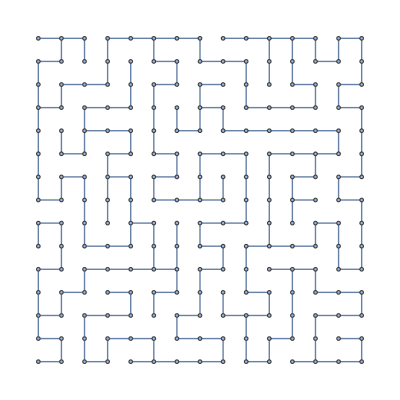
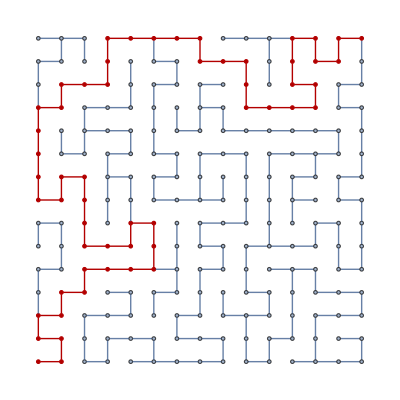
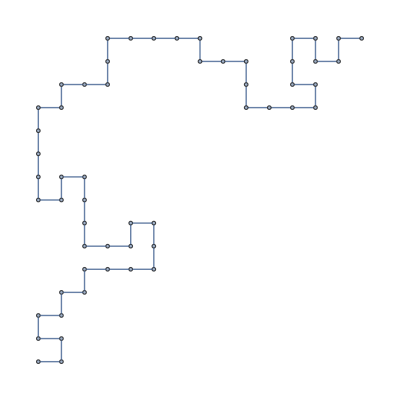
<|start→1,end→225,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→{1,16,17,2,3,18,19,34,35,50,65,80,81,82,67,66,51,36,37,38,39,24,23,8,9,10,11,12,27,28,43,58,59,60,75,90,105,120,119,134,149,148,147,162,177,192,193,178,179,180,195,194,209,210,225},distance→54,shortest-path-subgraph→-Graphics-,random-seed→RandomGeneratorState[…],tree→-Graphics-,tree-depth→102,tree-leaves→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},tree-leaf-count→21,tree-size→225,dead-ends→{6,15,26,44,49,52,61,74,78,97,102,124,129,133,135,155,163,166,172,188,197},dead-ends-count→21,tree-outline→|>

```mathematica
SeedRandom[randomSeed];
FindRandomGridMazeSolution[{15,15}]
```

### Scope

#### RandomSeed

Get just the random seed:

```mathematica
FindRandomGridMazeSolution[{150,150},"random-seed"]
```

<|random-seed→RandomGeneratorState[…]|>

Even for really big mazes, this doesn't slow the function down:

```mathematica
FindRandomGridMazeSolution[{1500,1500},"random-seed"]
```

<|random-seed→RandomGeneratorState[…]|>

#### Start

Get just the start:

```mathematica
FindRandomGridMazeSolution[{1500,1500},"start"]
```

<|start→1|>

#### End

Get just the end:

```mathematica
FindRandomGridMazeSolution[{1500,1500},"end"]
```

<|end→2250000|>

#### Maze

Get just the maze:

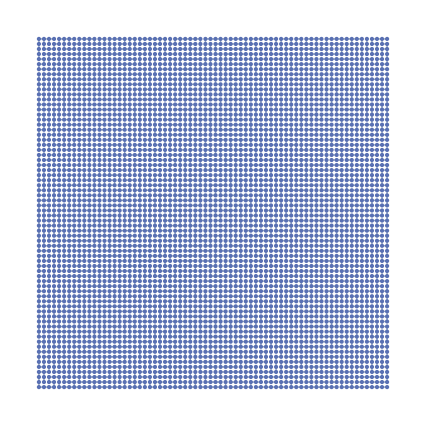
<|maze→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{70,70},"maze"]
```

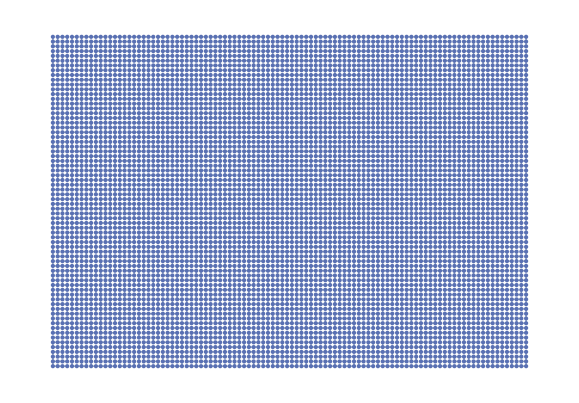
<|maze→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{70,100},"maze"]
```

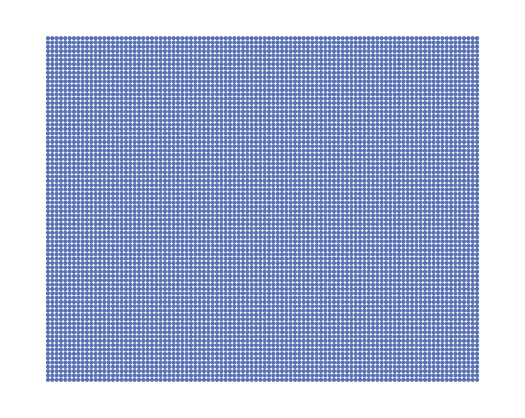
<|maze→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{80,100},"maze"]
```

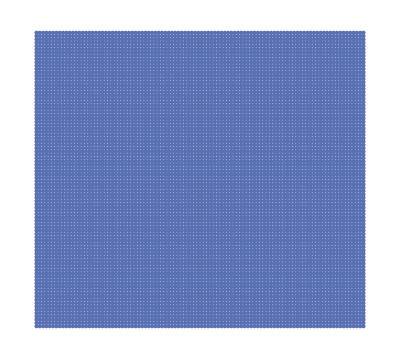
<|maze→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{90,100},"maze"]
```

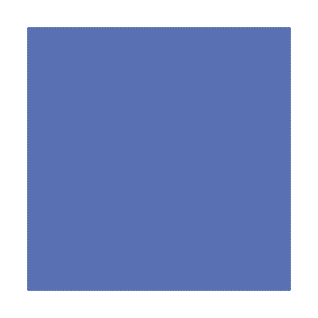
{2.64303,<|maze→-Graphics-|>}

```mathematica
RepeatedTiming@FindRandomGridMazeSolution[{100,100},"maze"]
```

Make a rectangular maze, which RandomMaze does not support.

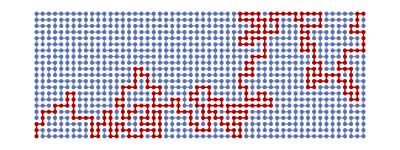

```mathematica
FindRandomGridMazeSolution[{21,54},"solved-maze"]
```

Make mazes fast:

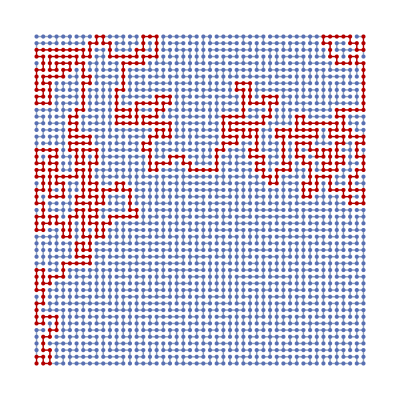

```mathematica
FindRandomGridMazeSolution[{50,50},"solved-maze"]
```

```mathematica
FindRandomGridMazeSolution[{100,100},"solved-maze"]
```

$RecursionLimit::reclim2: Recursion depth of 4096 exceeded during evaluation of ….

TreeDepth::tree: Tree expected at position 1 in ….

TreeLeaves::tree: Tree expected at position 1 in ….

TreeLeafCount::tree: Tree expected at position 1 in ….

TreeSize::tree: Tree expected at position 1 in ….

TreeLevel::tree: Tree expected at position 1 in ….

Complement::heads: Heads List and TreeLevel at positions 2 and 1 are expected to be the same.

TreeOutline::tree: Tree expected at position 1 in ….

Interrupted

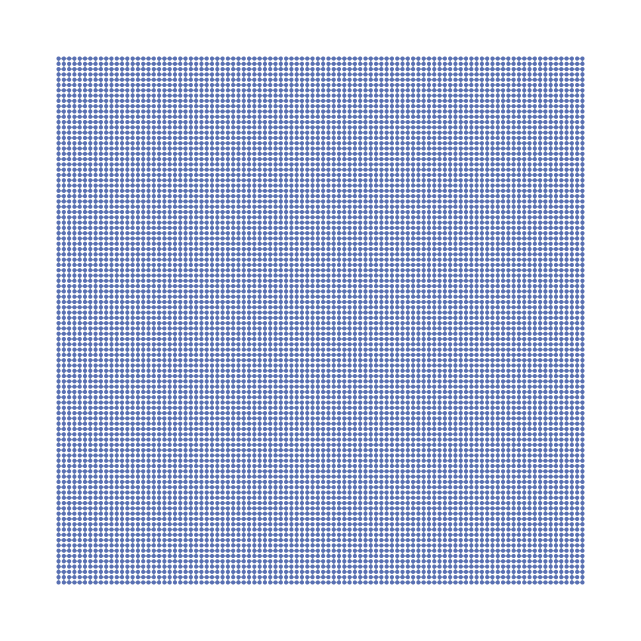
```mathematica
TreeGraphQ[-Graphics-]
```

True

```mathematica
GraphTree[CompleteKaryTree[3,5]]
```

-Graphics-

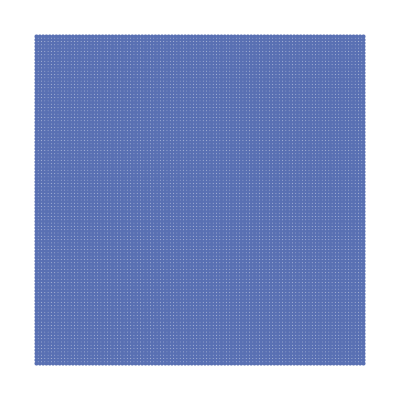
```mathematica
NeighborhoodGraph[-Graphics-,5000,200]
```

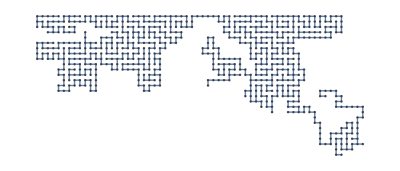

```mathematica
GraphTree[NeighborhoodGraph[-Graphics-,5000,200]]
```

-Graphics-

### Applications

Find a solution to a random 20 by 20 maze:

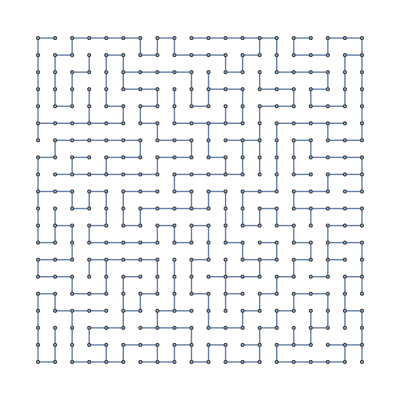
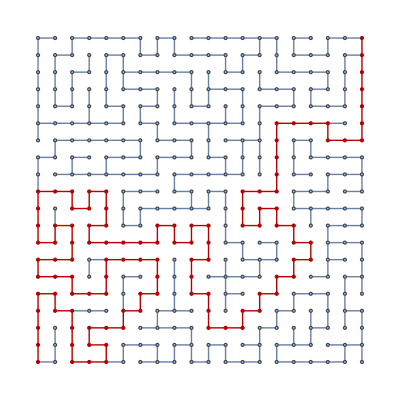
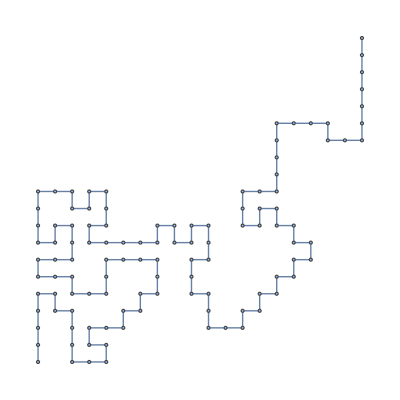
<|start→1,end→400,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→{1,2,3,4,5,25,24,44,43,42,41,61,81,82,62,63,83,103,104,124,125,145,146,147,127,107,87,86,85,65,45,46,26,6,7,27,47,48,49,29,28,8,9,10,11,31,51,50,70,71,91,90,89,69,68,88,108,128,148,149,169,168,188,189,209,208,207,187,186,185,205,204,203,223,243,244,264,265,285,286,306,307,327,328,308,309,289,290,270,269,249,250,251,271,291,292,293,294,295,315,335,355,354,374,394,395,396,397,398,399,400},distance→110,shortest-path-subgraph→-Graphics-,random-seed→RandomGeneratorState[…],tree→-Graphics-,tree-depth→151,tree-leaves→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},tree-leaf-count→42,tree-size→400,dead-ends→{14,23,30,32,40,66,73,77,79,84,121,123,126,151,167,177,184,200,206,218,224,227,234,236,242,245,268,272,278,303,324,326,329,332,340,342,363,367,371,375,381,385},dead-ends-count→42,tree-outline→|>

```mathematica
FindRandomGridMazeSolution[{20,20}]
```

Find a solution to a random 50 by 60 maze:

```mathematica
FindRandomGridMazeSolution[{50,60}]
```

-Graphics-

Find a solution to a random 60 by 70 maze:

```mathematica
FindRandomGridMazeSolution[{60,70}]
```

-Graphics-

Solve a random 70 by 80 maze:

```mathematica
FindRandomGridMazeSolution[{70,80}]
```

-Graphics-

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

mazes

graph algorithms

fun

### Categories

Cloud & Deployment
 External Interfaces & Connections
 Graphs & Networks
 Knowledge Representation & Natural Language
 Repository Tools
 Strings & Text
 User Interface Construction |  Core Language & Structure
 Financial Data & Computation
 Higher Mathematical Computation
 Machine Learning
 Scientific and Medical Data & Computation
 Symbolic & Numeric Computation
 Visualization & Graphics |  Data Manipulation & Analysis
 Geographic Data & Computation
 Images
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 System Operation & Setup
 Wolfram Physics Project |  Engineering Data & Computation
 Geometry
 Just For Fun
 Programming Utilities
 Sound & Video
 Time-Related Computation

### Related Symbols

FindShortestPath

### Related Resource Objects

RandomMaze

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.